```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

```mathematica
TrigReduce[Cos[0.3 t] Sin[0.03 t]]
```

1/2 (-Sin[(0.27+0. ⅈ) t]+Sin[(0.33+0. ⅈ) t])

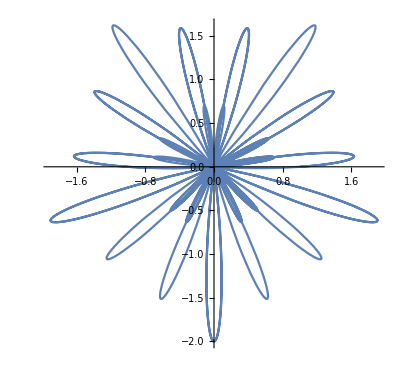

```mathematica
ParametricPlot[{(Cos[0.2 t ]+Sin[0.3 t]) Cos[0.02t],(Cos[0.2 t ]+Sin[0.3 t]) Sin[0.02 t] },{t,0,500}]
```

can

ReplaceAll::reps: {can} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

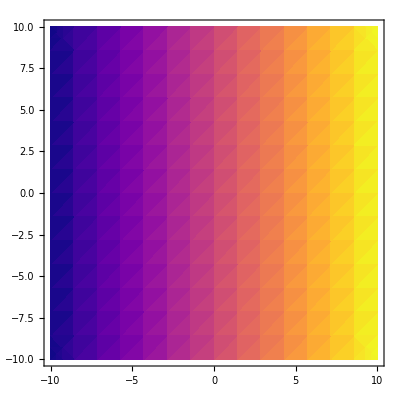

```mathematica
para=can[[]]
sol1=roller[para];
sol2=rollerflat[para];
Show[DensityPlot[x,{x,-10,10},{y,-10,10},ColorFunction->MPLColorMap["Plasma"]],
ParametricPlot[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,5000},PlotStyle->{White, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
ParametricPlot[{x[t]/.sol2[[1]],y[t]/.sol2[[1]]},{t,0,5000},PlotStyle->{Red, AbsoluteThickness[2]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False]

]
```

```mathematica
B[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_},t_]:={(B1 Cos[t ωB1 ]+B2*Cos[ωB2 t ])*Sin[ω4 t],(B1 Cos[t ωB1 ]+B2*Cos[ωB1 t ])*Cos[ω4 t], (A1 Sin[t ωA1 ]+A2*Sin[ωA2 t ])}.RotationMatrix[10 Degree ,{0,1,0}];

Bflat[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_},t_]:={(B1 Cos[t ωB1 ]+B2*Cos[ωB2 t ])*Sin[ω4 t],(B1 Cos[t ωB1 ]+B2*Cos[ωB1 t ])*Cos[ω4 t], (A1 Sin[t ωA1 ]+A2*Sin[ωA2 t ])};
```

```mathematica
roller[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ωA1,ωA2,A1,A2,ωB1,ωB2,B1, B2,ω4};
tMax = (*Min[200 2 π/parameter[[1]],50000.0]*0+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]
rollerflat[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ωA1,ωA2,A1,A2,ωB1,ωB2,B1, B2,ω4};
tMax =(* Min[200 2 π/parameter[[1]],50000.0]+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,Bflat[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]


(*B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]*)
```

```mathematica
Min[2,3]
```

2

```mathematica
can={};
For [i=0,i<1000,
ωA1=RandomReal[{0.1,0.4}];
ωA2=RandomReal[{ωA1,1}];
A1=RandomReal[{-2,2}];
A2=RandomReal[{-2,2}];
ωB1=RandomReal[{ωA1*0.8,ωA1*1.2}];
ωB2=RandomReal[{ωB1,1}];
B1=RandomReal[{-2,2}];
B2=RandomReal[{-2,2}];
ω4=Min[ωA1,ωB1]/RandomReal[{10,30}];
sol1=roller[{ωA1,ωA2,A1,A2,ωB1,ωB2,B1, B2,ω4}];
sol2=rollerflat[{ωA1,ωA2,A1,A2,ωB1,ωB2,B1,B2,ω4}];
bias=Table[x[t]/.sol1[[1]],{t,1,5000}];
flat=Table[x[t]/.sol2[[1]],{t,1,5000}];
If[(Min[flat]-Min[bias]>1)&&(Abs[Min[bias]/(y[t]/.sol1[[1]]/.t->Ordering[bias,1][[1]])]>0.35), can =Append[can,{ωA1,ωA2,A1,A2,ωB1,ωB2,B1, B2,ω4}]];
i++
]
```

ω1

```mathematica
can
```

{{0.214044,0.266526,0.228329,0.120167,0.213001,0.280463,-1.65634,1.34668,0.00794416},{0.345866,0.694031,-0.236022,1.44615,0.37296,0.526603,1.77745,-0.776428,0.0219913},{0.126971,0.988288,-0.0996929,-1.10134,0.122823,0.130318,1.48236,-1.75173,0.00614546},{0.3458,0.830343,0.0363551,0.835714,0.385661,0.537295,1.54175,1.72298,0.0221163},{0.250099,0.854439,-0.576571,0.361114,0.204843,0.528932,-1.04399,-1.35627,0.0161782},{0.240817,0.488625,-0.277124,-0.379966,0.197894,0.27245,-0.179941,-1.743,0.00786196},{0.248296,0.950521,-0.190935,0.664109,0.221127,0.774805,1.69643,1.64401,0.00938229},{0.302766,0.787093,-0.0577345,1.26537,0.33727,0.515435,-0.843769,-0.568026,0.0253448},{0.369679,0.896714,0.0750034,-1.47734,0.420765,0.99559,-1.89276,0.810569,0.022923},{0.166842,0.32546,0.106856,0.309884,0.169391,0.601828,1.505,-1.9633,0.00930142},{0.267518,0.42897,-0.623857,-0.344841,0.246831,0.414894,-0.473004,-1.96839,0.00960572},{0.11374,0.750466,-0.0463087,-1.01324,0.114032,0.253813,-1.03482,1.28481,0.00520061},{0.266584,0.734254,0.200081,-0.409973,0.258102,0.63307,-1.13101,-1.55989,0.0155917},{0.143991,0.921778,0.114586,0.635684,0.153759,0.232648,-1.39377,-0.40631,0.00548433},{0.209413,0.894023,-0.378774,0.756195,0.207055,0.947575,1.72339,1.55841,0.0083725},{0.309178,0.930841,0.0378922,0.261207,0.331399,0.745509,1.86234,1.71897,0.0204519},{0.397836,0.492153,0.420218,-0.894773,0.474822,0.801836,-1.43255,1.07848,0.0384425},{0.293363,0.973597,0.0676479,0.348266,0.246707,0.276051,-1.67419,-1.05271,0.0111663},{0.334982,0.475739,0.0867991,1.26136,0.271619,0.984185,0.85435,0.00757863,0.0156872},{0.271908,0.624908,0.0423387,-0.0290267,0.236122,0.4704,1.63452,-1.03514,0.0159599},{0.372628,0.515141,-0.089405,0.600952,0.309408,0.474709,0.574065,-1.8748,0.0148975},{0.168131,0.768962,-0.0267705,1.42927,0.154977,0.446007,1.75656,0.376932,0.0143779},{0.218351,0.537049,0.751691,-0.231421,0.254739,0.65341,1.47219,1.35385,0.0152484},{0.346652,0.492251,-0.566269,-0.55132,0.317507,0.56863,1.59603,1.48979,0.0154762},{0.259237,0.669614,0.356663,1.05067,0.291654,0.970055,-1.81962,-1.81251,0.0130326},{0.18887,0.997984,0.0732416,0.0355292,0.193607,0.903363,-0.742609,-1.98668,0.0124405},{0.32793,0.809535,0.193013,0.415463,0.300508,0.721208,1.53367,-0.0746738,0.0231177},{0.349409,0.828258,0.365182,1.86035,0.402066,0.47709,-1.74058,0.307339,0.0258827},{0.358127,0.737896,0.202694,0.916281,0.315001,0.443198,-1.21316,-1.70091,0.0137694},{0.351008,0.526768,-0.053663,-0.864353,0.412771,0.749294,-1.90883,-1.78774,0.0182105},{0.138492,0.889371,-0.517089,0.450822,0.124537,0.453234,0.883435,1.77926,0.00531972},{0.183534,0.821354,0.798634,0.778725,0.185619,0.654742,0.26774,-1.9819,0.0182505},{0.385169,0.810914,-0.449185,0.445451,0.311384,0.335218,1.44033,1.36367,0.0216298},{0.275469,0.891608,0.0889085,-1.48515,0.243822,0.297152,0.686697,-1.62819,0.0150066},{0.113286,0.31336,0.206657,-0.0854761,0.103306,0.821535,-0.12925,-1.85885,0.00437677},{0.223448,0.833726,0.166194,-1.86623,0.235159,0.508907,-1.62882,0.641596,0.0164436},{0.136489,0.280329,0.242143,-0.729484,0.152328,0.556535,-0.0740387,1.90829,0.00486098},{0.107558,0.282418,0.332309,-0.537505,0.107203,0.314601,-1.31975,-1.43295,0.01052},{0.255023,0.824038,-0.216922,0.551387,0.276618,0.661787,0.565935,1.78715,0.00889749},{0.214725,0.56485,0.277165,-0.488629,0.251046,0.968381,1.87013,1.81809,0.0175874},{0.131528,0.562289,0.428503,-1.08602,0.147161,0.445931,0.171105,-1.80767,0.00782319},{0.311769,0.624154,0.219176,-1.94356,0.249986,0.453698,-1.25349,0.163359,0.010555},{0.287645,0.516589,-0.288381,-0.269304,0.316804,0.446063,-0.969301,1.94142,0.0236802},{0.269529,0.627166,0.397389,1.14546,0.244416,0.850943,1.15735,-1.39842,0.0165494},{0.220633,0.554769,0.360312,1.64682,0.214991,0.943457,1.17216,-0.321503,0.0207453},{0.187242,0.502063,-0.302271,0.354496,0.220467,0.272256,1.48571,0.639909,0.0135994},{0.258931,0.800193,0.134116,1.16707,0.216292,0.24378,1.59703,-0.134882,0.0116407},{0.362711,0.408659,0.81555,-0.813069,0.338167,0.445217,-1.64804,1.9492,0.0277036},{0.179191,0.419634,0.15559,0.00414892,0.176267,0.307826,-1.52965,-1.88171,0.0102815},{0.342194,0.757354,-0.291274,-0.291512,0.278458,0.427913,1.06093,0.84333,0.00974484},{0.105194,0.181763,1.06915,-0.0542924,0.0842548,0.485069,-0.20876,1.83362,0.00727161},{0.399266,0.909819,-0.0346327,1.5166,0.447928,0.864198,1.48753,-0.724824,0.015293},{0.318499,0.745328,-0.702922,0.274689,0.323835,0.936847,1.52434,1.74867,0.0193995},{0.379758,0.832551,0.218682,-0.377308,0.342052,0.478956,-0.0498309,-1.96454,0.0229811},{0.24628,0.46477,0.183412,-0.699262,0.20103,0.859659,-0.626342,1.53112,0.0160863},{0.188475,0.586526,-0.157648,-0.459813,0.200783,0.752047,-1.25482,-0.0895472,0.0129899},{0.222313,0.86185,-0.342651,-0.620237,0.216857,0.601726,1.34577,1.40946,0.0104766},{0.356554,0.678613,0.193166,-0.147492,0.335812,0.447684,-1.95296,-1.71464,0.0123303},{0.280766,0.758125,-0.196225,1.04146,0.23431,0.380979,1.61424,-1.92612,0.0132115},{0.267136,0.713167,0.405197,-0.779431,0.286908,0.342275,-1.86679,1.98583,0.00907466},{0.39475,0.93276,0.155662,-0.42664,0.328175,0.342762,0.50294,-1.4233,0.0285239},{0.140868,0.547585,0.0325509,0.0507147,0.120784,0.484137,-1.13523,-0.0772569,0.0110866},{0.180727,0.709575,-0.132365,1.31291,0.186648,0.255393,0.965895,-1.46636,0.00840886},{0.328239,0.64901,0.291233,-1.79069,0.330784,0.635511,-1.48493,0.598253,0.0131423},{0.345367,0.802529,-0.102718,-1.4017,0.41364,0.439088,1.50893,-0.000772801,0.0165175},{0.152586,0.442006,0.00619934,-0.452075,0.126485,0.454756,1.99753,-1.47321,0.00445458},{0.205683,0.954266,-0.298591,0.217695,0.198914,0.312163,1.63226,-1.94066,0.0182693},{0.352466,0.970145,-0.645299,0.848736,0.285296,0.883221,-1.73203,-1.58493,0.0104344},{0.234221,0.771663,0.187954,0.144596,0.188101,0.504661,1.44289,-1.1671,0.0154493}}

```mathematica
Length[can]
```

69

12.8481

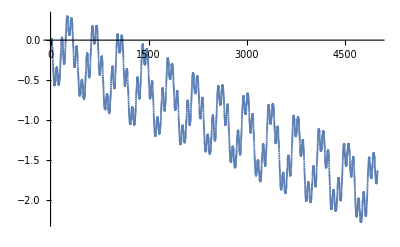

{s,s}

```mathematica
ListPlot[flat]
```

```mathematica
Export["can.csv",can]
```

can.csv

```mathematica
(*B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]*)
```

```mathematica
para=can[[70]]
sol1=roller[para];
sol2=rollerflat[para];
Show[DensityPlot[x,{x,-10,10},{y,-10,10},ColorFunction->MPLColorMap["Plasma"]],
ParametricPlot[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,5000},PlotStyle->{White, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
ParametricPlot[{x[t]/.sol2[[1]],y[t]/.sol2[[1]]},{t,0,5000},PlotStyle->{Red, AbsoluteThickness[2]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False]

]
```

Part::partw: Part 70 of {{0.214044,0.266526,0.228329,0.120167,0.213001,0.280463,-1.65634,1.34668,0.00794416},{0.345866,0.694031,-0.236022,1.44615,0.37296,0.526603,1.77745,-0.776428,0.0219913},«47»,{0.342194,0.757354,-0.291274,-0.291512,0.278458,0.427913,1.06093,0.84333,0.00974484},«19»} does not exist.

{{0.214044,0.266526,0.228329,0.120167,0.213001,0.280463,-1.65634,1.34668,0.00794416},{0.345866,0.694031,-0.236022,1.44615,0.37296,0.526603,1.77745,-0.776428,0.0219913},{0.126971,0.988288,-0.0996929,-1.10134,0.122823,0.130318,1.48236,-1.75173,0.00614546},{0.3458,0.830343,0.0363551,0.835714,0.385661,0.537295,1.54175,1.72298,0.0221163},{0.250099,0.854439,-0.576571,0.361114,0.204843,0.528932,-1.04399,-1.35627,0.0161782},{0.240817,0.488625,-0.277124,-0.379966,0.197894,0.27245,-0.179941,-1.743,0.00786196},{0.248296,0.950521,-0.190935,0.664109,0.221127,0.774805,1.69643,1.64401,0.00938229},{0.302766,0.787093,-0.0577345,1.26537,0.33727,0.515435,-0.843769,-0.568026,0.0253448},{0.369679,0.896714,0.0750034,-1.47734,0.420765,0.99559,-1.89276,0.810569,0.022923},{0.166842,0.32546,0.106856,0.309884,0.169391,0.601828,1.505,-1.9633,0.00930142},{0.267518,0.42897,-0.623857,-0.344841,0.246831,0.414894,-0.473004,-1.96839,0.00960572},{0.11374,0.750466,-0.0463087,-1.01324,0.114032,0.253813,-1.03482,1.28481,0.00520061},{0.266584,0.734254,0.200081,-0.409973,0.258102,0.63307,-1.13101,-1.55989,0.0155917},{0.143991,0.921778,0.114586,0.635684,0.153759,0.232648,-1.39377,-0.40631,0.00548433},{0.209413,0.894023,-0.378774,0.756195,0.207055,0.947575,1.72339,1.55841,0.0083725},{0.309178,0.930841,0.0378922,0.261207,0.331399,0.745509,1.86234,1.71897,0.0204519},{0.397836,0.492153,0.420218,-0.894773,0.474822,0.801836,-1.43255,1.07848,0.0384425},{0.293363,0.973597,0.0676479,0.348266,0.246707,0.276051,-1.67419,-1.05271,0.0111663},{0.334982,0.475739,0.0867991,1.26136,0.271619,0.984185,0.85435,0.00757863,0.0156872},{0.271908,0.624908,0.0423387,-0.0290267,0.236122,0.4704,1.63452,-1.03514,0.0159599},{0.372628,0.515141,-0.089405,0.600952,0.309408,0.474709,0.574065,-1.8748,0.0148975},{0.168131,0.768962,-0.0267705,1.42927,0.154977,0.446007,1.75656,0.376932,0.0143779},{0.218351,0.537049,0.751691,-0.231421,0.254739,0.65341,1.47219,1.35385,0.0152484},{0.346652,0.492251,-0.566269,-0.55132,0.317507,0.56863,1.59603,1.48979,0.0154762},{0.259237,0.669614,0.356663,1.05067,0.291654,0.970055,-1.81962,-1.81251,0.0130326},{0.18887,0.997984,0.0732416,0.0355292,0.193607,0.903363,-0.742609,-1.98668,0.0124405},{0.32793,0.809535,0.193013,0.415463,0.300508,0.721208,1.53367,-0.0746738,0.0231177},{0.349409,0.828258,0.365182,1.86035,0.402066,0.47709,-1.74058,0.307339,0.0258827},{0.358127,0.737896,0.202694,0.916281,0.315001,0.443198,-1.21316,-1.70091,0.0137694},{0.351008,0.526768,-0.053663,-0.864353,0.412771,0.749294,-1.90883,-1.78774,0.0182105},{0.138492,0.889371,-0.517089,0.450822,0.124537,0.453234,0.883435,1.77926,0.00531972},{0.183534,0.821354,0.798634,0.778725,0.185619,0.654742,0.26774,-1.9819,0.0182505},{0.385169,0.810914,-0.449185,0.445451,0.311384,0.335218,1.44033,1.36367,0.0216298},{0.275469,0.891608,0.0889085,-1.48515,0.243822,0.297152,0.686697,-1.62819,0.0150066},{0.113286,0.31336,0.206657,-0.0854761,0.103306,0.821535,-0.12925,-1.85885,0.00437677},{0.223448,0.833726,0.166194,-1.86623,0.235159,0.508907,-1.62882,0.641596,0.0164436},{0.136489,0.280329,0.242143,-0.729484,0.152328,0.556535,-0.0740387,1.90829,0.00486098},{0.107558,0.282418,0.332309,-0.537505,0.107203,0.314601,-1.31975,-1.43295,0.01052},{0.255023,0.824038,-0.216922,0.551387,0.276618,0.661787,0.565935,1.78715,0.00889749},{0.214725,0.56485,0.277165,-0.488629,0.251046,0.968381,1.87013,1.81809,0.0175874},{0.131528,0.562289,0.428503,-1.08602,0.147161,0.445931,0.171105,-1.80767,0.00782319},{0.311769,0.624154,0.219176,-1.94356,0.249986,0.453698,-1.25349,0.163359,0.010555},{0.287645,0.516589,-0.288381,-0.269304,0.316804,0.446063,-0.969301,1.94142,0.0236802},{0.269529,0.627166,0.397389,1.14546,0.244416,0.850943,1.15735,-1.39842,0.0165494},{0.220633,0.554769,0.360312,1.64682,0.214991,0.943457,1.17216,-0.321503,0.0207453},{0.187242,0.502063,-0.302271,0.354496,0.220467,0.272256,1.48571,0.639909,0.0135994},{0.258931,0.800193,0.134116,1.16707,0.216292,0.24378,1.59703,-0.134882,0.0116407},{0.362711,0.408659,0.81555,-0.813069,0.338167,0.445217,-1.64804,1.9492,0.0277036},{0.179191,0.419634,0.15559,0.00414892,0.176267,0.307826,-1.52965,-1.88171,0.0102815},{0.342194,0.757354,-0.291274,-0.291512,0.278458,0.427913,1.06093,0.84333,0.00974484},{0.105194,0.181763,1.06915,-0.0542924,0.0842548,0.485069,-0.20876,1.83362,0.00727161},{0.399266,0.909819,-0.0346327,1.5166,0.447928,0.864198,1.48753,-0.724824,0.015293},{0.318499,0.745328,-0.702922,0.274689,0.323835,0.936847,1.52434,1.74867,0.0193995},{0.379758,0.832551,0.218682,-0.377308,0.342052,0.478956,-0.0498309,-1.96454,0.0229811},{0.24628,0.46477,0.183412,-0.699262,0.20103,0.859659,-0.626342,1.53112,0.0160863},{0.188475,0.586526,-0.157648,-0.459813,0.200783,0.752047,-1.25482,-0.0895472,0.0129899},{0.222313,0.86185,-0.342651,-0.620237,0.216857,0.601726,1.34577,1.40946,0.0104766},{0.356554,0.678613,0.193166,-0.147492,0.335812,0.447684,-1.95296,-1.71464,0.0123303},{0.280766,0.758125,-0.196225,1.04146,0.23431,0.380979,1.61424,-1.92612,0.0132115},{0.267136,0.713167,0.405197,-0.779431,0.286908,0.342275,-1.86679,1.98583,0.00907466},{0.39475,0.93276,0.155662,-0.42664,0.328175,0.342762,0.50294,-1.4233,0.0285239},{0.140868,0.547585,0.0325509,0.0507147,0.120784,0.484137,-1.13523,-0.0772569,0.0110866},{0.180727,0.709575,-0.132365,1.31291,0.186648,0.255393,0.965895,-1.46636,0.00840886},{0.328239,0.64901,0.291233,-1.79069,0.330784,0.635511,-1.48493,0.598253,0.0131423},{0.345367,0.802529,-0.102718,-1.4017,0.41364,0.439088,1.50893,-0.000772801,0.0165175},{0.152586,0.442006,0.00619934,-0.452075,0.126485,0.454756,1.99753,-1.47321,0.00445458},{0.205683,0.954266,-0.298591,0.217695,0.198914,0.312163,1.63226,-1.94066,0.0182693},{0.352466,0.970145,-0.645299,0.848736,0.285296,0.883221,-1.73203,-1.58493,0.0104344},{0.234221,0.771663,0.187954,0.144596,0.188101,0.504661,1.44289,-1.1671,0.0154493}}⟦70⟧

ReplaceAll::reps: {{{0.214044,0.266526,0.228329,0.120167,0.213001,0.280463,-1.65634,1.34668,0.00794416},{0.345866,0.694031,-0.236022,1.44615,0.37296,0.526603,1.77745,-0.776428,0.0219913},«47»,{0.342194,0.757354,-0.291274,-0.291512,0.278458,0.427913,1.06093,0.84333,0.00974484},«19»}⟦70⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

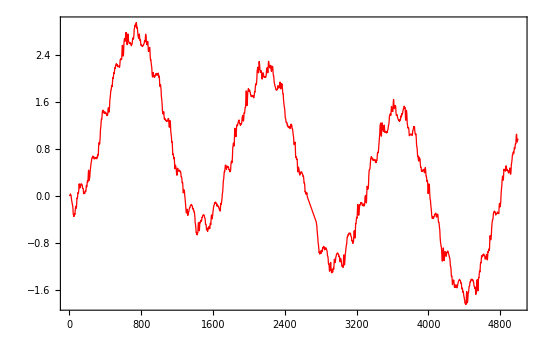

```mathematica
Plot[x[t]/.sol1[[1]],{t,0,5000},PlotStyle->{Red, AbsoluteThickness[0.9]},Frame->True,Axes->False]
```

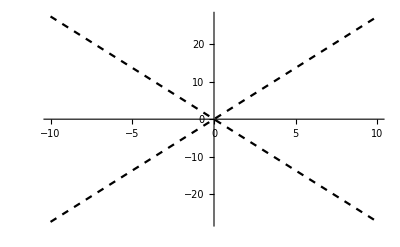

```mathematica
Plot[{Cot[20 Degree]x,-Cot[20 Degree]x},{x,-10,10},PlotStyle->{{Dashed,Black},{Dashed,Black}}]
```

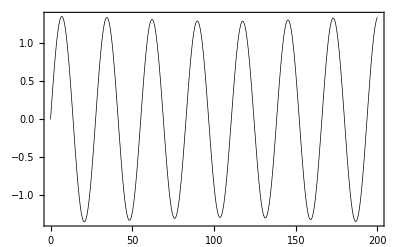

```mathematica
Afield[{ωA1_,ωA2_,A1_,A2_},t_]:=A1 Sin[ωA1 t ]+A2 Sin[ωA2 t ]
Bfield[{ωB1_,ωB2_,B1_,B2_},t_]:=B1 Sin[ωB1 t ]+B2 Sin[ωB2 t ]
Plot[zfield[Pick[para,{1,1,0,1,1,0,0},1],t],{t,0,200},Frame->True,PlotStyle->{Black, AbsoluteThickness[0.5]}]
```

```mathematica
{0.511610972251507,0.7908980392500011,0.9721937181040985,0.018303814988236116,-0.27558310463922453,0.007526608200789653,0.06897963832795106,-1.1096269873188795,-1.4979572111557324}


{0.22872562558307657,0.6043588891674827,1.7043856680115557,0.01324038768746723,-0.5900082271963392,1.6908331541215453,-0.3248939705669116,1.2352178961027764,1.6531395301189313}
```

```mathematica
Pick[can[[2]],{1,1,1,0,1,1,1,0,0},1]
```

{0.114839,0.547198,0.704085,-0.317738,0.0414221,0.144293}

{0.114839,0.547198,0.704085}

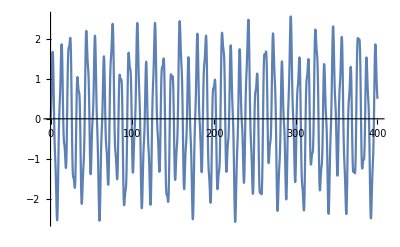

```mathematica
can[[2]][[1;;3]]
```

```mathematica
522/97.0
```

5.38144

```mathematica
{ 0.5Cos[0.18 t]+0.5 Cos[0.22 t],0, 0.2 Sin[0.2 t]}.RotationMatrix[10.0 Degree ,{0,1,0}]
```

{0.+0.984808 (0.5 Cos[0.18 t]+0.5 Cos[0.22 t])-0.0347296 Sin[0.2 t],0.,0.+0.173648 (0.5 Cos[0.18 t]+0.5 Cos[0.22 t])+0.196962 Sin[0.2 t]}

{0.+0.984808 (0.5 Cos[0.1 t]+0.5 Cos[0.2 t])-0.173648 Sin[0.2 t],0.,0.+0.173648 (0.5 Cos[0.1 t]+0.5 Cos[0.2 t])+0.984808 Sin[0.2 t]}

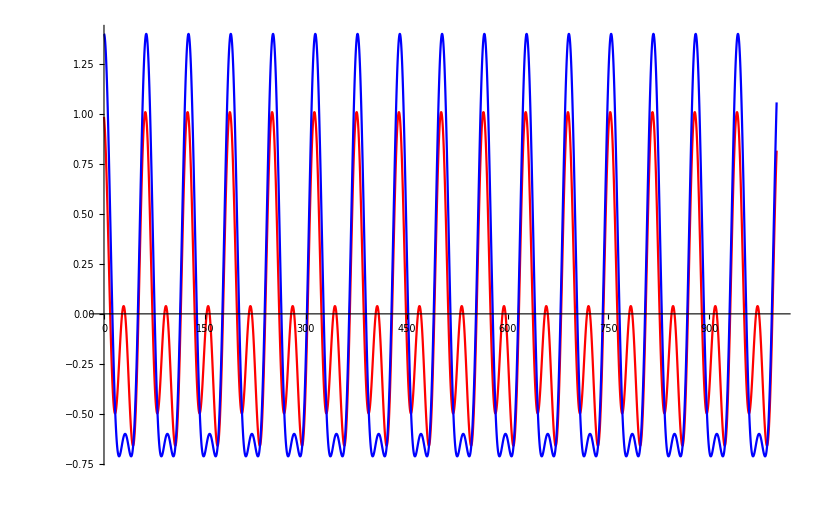

```mathematica
{ 0.5Cos[0.1 t]+0.5 Cos[0.2 t],0,   Sin[0.2 t] }.RotationMatrix[10.0 Degree ,{0,1,0}]
Plot[{%[[1]], Cos[0.1 t]+0.4 Cos[0.2 t] },{t,0,1000},PlotStyle->{Red, Blue}]
```

```mathematica
0.5Cos[0.19 t]+0.5 Cos[0.21 t]
```